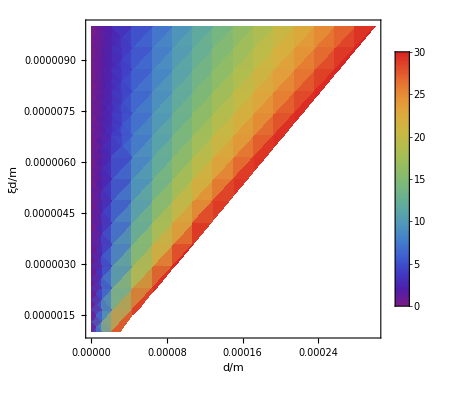

~/Downloads/1.pdf

```mathematica
DensityPlot[d/ξd,{d,0,3*10^-4},{ξd,10^-6,10^-5},ColorFunction->"Rainbow",PlotRange->{0,30},PlotLegends->Automatic,Axes->True,AxesOrigin->{1.5*10^-4,5*10^-6},AxesLabel->{"d/m","ξd/m"}]
Export["~/Downloads/1.pdf",%]
```

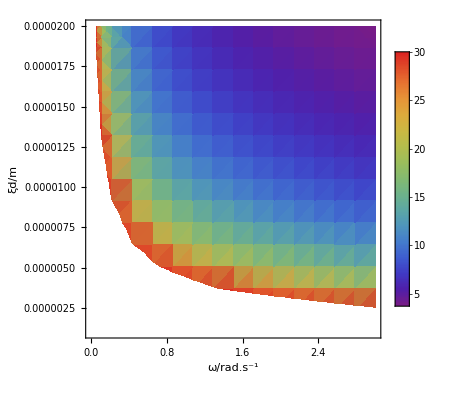

~/Downloads/1.pdf

```mathematica
DensityPlot[(√((0.5 κ0)/(2 ω)))/ξd/.{κ0->6.61*10^-8},{ω,0,3},{ξd,10^-6,2*10^-5},ColorFunction->"Rainbow",PlotRange->{0,30},PlotLegends->Automatic,Axes->True,AxesOrigin->{1.5,5*10^-6},AxesLabel->{"ω/rad.s^-1","ξd/m"}]
Export["~/Downloads/1.pdf",%]
```

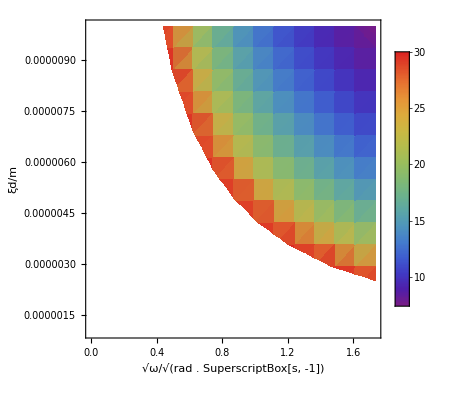

~/Downloads/1.pdf

```mathematica
DensityPlot[(√((0.5 κ0)/(2 (sqω^2))))/ξd/.{κ0->6.61*10^-8},{sqω,0,√3},{ξd,10^-6,1*10^-5},ColorFunction->"Rainbow",PlotRange->{0,30},PlotLegends->Automatic,Axes->True,AxesOrigin->{1.5,5*10^-6},AxesLabel->{"√ω/√(rad . SuperscriptBox[s, -1])","ξd/m"}]
Export["~/Downloads/1.pdf",%]
```

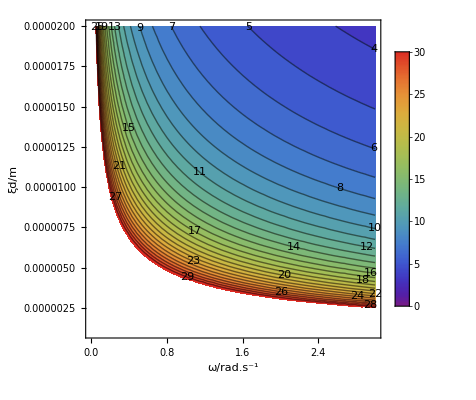

~/Downloads/1.pdf

```mathematica
ContourPlot[(√((0.5 κ0)/(2 ω)))/ξd/.{κ0->6.61*10^-8},{ω,0,3},{ξd,10^-6,2*10^-5},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0,30},Contours->Function[{min,max},Range[min,max,1]],ContourLabels->True,Axes->True,AxesOrigin->{1.5,5*10^-6},AxesLabel->{"ω/rad.s^-1","ξd/m"}]
Export["~/Downloads/1.pdf",%]
```

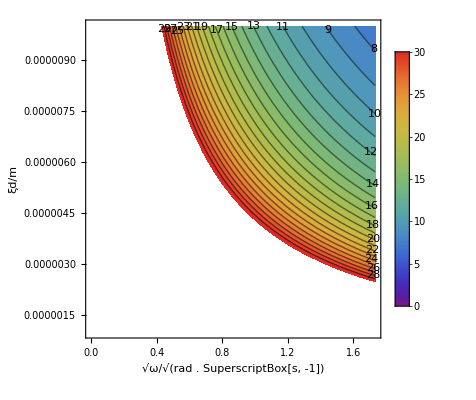

~/Downloads/2.pdf

```mathematica
ContourPlot[(√((0.5 κ0)/(2 (sqω^2))))/ξd/.{κ0->6.61*10^-8},{sqω,0,√3},{ξd,10^-6,1*10^-5},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotRange->{0,30},Contours->Function[{min,max},Range[min,max,1]],ContourLabels->True,Axes->True,AxesOrigin->{1.5,5*10^-6},AxesLabel->{"√ω/√(rad . SuperscriptBox[s, -1])","ξd/m"}]
Export["~/Downloads/2.pdf",%]
```